```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2"];
```

```mathematica
(* symptom combinations *)
```

```mathematica
combodata=Import["catanxmc1e6_4cat_8sym_unif\\_freq-4_8_unif-spreads-cat_anxiety-sym_combo.csv"];
```

```mathematica
combodata[[1]]
```

{cat_1_N,cat_1_O,cat_1_M,cat_1_T,cat_1_OM,cat_1_OT,cat_1_MT,cat_1_OMT,cat_2_N,cat_2_O,cat_2_M,cat_2_T,cat_2_OM,cat_2_OT,cat_2_MT,cat_2_OMT,cat_3_N,cat_3_O,cat_3_M,cat_3_T,cat_3_OM,cat_3_OT,cat_3_MT,cat_3_OMT,cat_4_N,cat_4_O,cat_4_M,cat_4_T,cat_4_OM,cat_4_OT,cat_4_MT,cat_4_OMT}

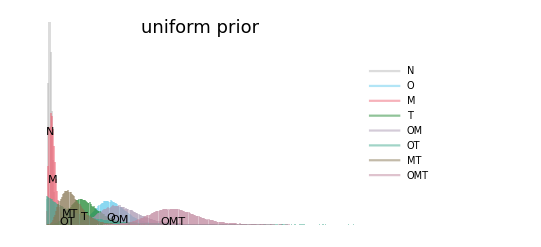

```mathematica
cat=4;
data=combodata[[2;;,-8-8*(4-cat);;-1-8*(4-cat)]];
names={"N","O","M","T","OM","OT","MT","OMT"};
positions=Table[hd=HistogramDistribution[T[data][[i]],"FreedmanDiaconis"];
mhd=Median[hd];{mhd,PDF[hd,mhd]*0.5},{i,8}];
cols={blue,red,green};
colours=Flatten@{grey,Sequence@cols,Blend[cols[[{1,2}]],0.5],Blend[cols[[{1,3}]],0.5],Blend[cols[[{2,3}]],0.5],Blend[cols[[{1,2,3}]],1/3]};
plot=Histogram[T[data],"FreedmanDiaconis","PDF",
ChartStyle->colours,ChartLegends->mylegends[Evaluate[Style[#,18]&/@names],{0.5,0.9}],
(*ChartLabels->Placed[Evaluate[Style[#,12]&/@names],Auto],*)
FrameLabel->{"frequency of anxiety category #"<>ToString[cat],"density"},ImageSize->a4longside,PlotRange->{All,All},Epilog->Evaluate[Flatten@{Text[Style["uniform prior",18],Scaled[{0.5,1}],{0,1}],Table[Text[names[[i]],positions[[i]],{0,1}],{i,8}]}]]
```

```mathematica
Export["anxcat"<>ToString[cat]<>"_symptomcombos_unif.pdf",plot,Magnification->1,ImageResolution->400]
```

anxcat4_symptomcombos_unif.pdf

```mathematica
combodata=Import["catanxmc1e6_4cat_8sym_cons\\_freq-4_8_cons-spreads-cat_anxiety-sym_combo.csv"];
```

```mathematica
combodata[[1]]
```

{cat_1_N,cat_1_O,cat_1_M,cat_1_T,cat_1_OM,cat_1_OT,cat_1_MT,cat_1_OMT,cat_2_N,cat_2_O,cat_2_M,cat_2_T,cat_2_OM,cat_2_OT,cat_2_MT,cat_2_OMT,cat_3_N,cat_3_O,cat_3_M,cat_3_T,cat_3_OM,cat_3_OT,cat_3_MT,cat_3_OMT,cat_4_N,cat_4_O,cat_4_M,cat_4_T,cat_4_OM,cat_4_OT,cat_4_MT,cat_4_OMT}

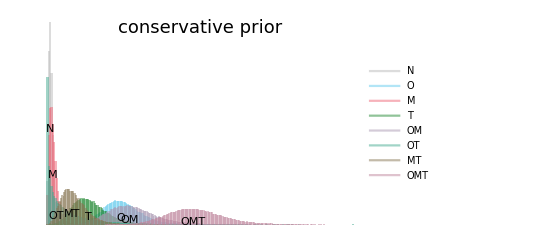

```mathematica
cat=4;
data=combodata[[2;;,-8-8*(4-cat);;-1-8*(4-cat)]];
names={"N","O","M","T","OM","OT","MT","OMT"};
positions=Table[hd=HistogramDistribution[T[data][[i]],"FreedmanDiaconis"];
mhd=Median[hd];{mhd,PDF[hd,mhd]*0.5},{i,8}];
cols={blue,red,green};
colours=Flatten@{grey,Sequence@cols,Blend[cols[[{1,2}]],0.5],Blend[cols[[{1,3}]],0.5],Blend[cols[[{2,3}]],0.5],Blend[cols[[{1,2,3}]],1/3]};
plot=Histogram[T[data],"FreedmanDiaconis","PDF",
ChartStyle->colours,ChartLegends->mylegends[Evaluate[Style[#,18]&/@names],{0.5,0.9}],
(*ChartLabels->Placed[Evaluate[Style[#,12]&/@names],Auto],*)
FrameLabel->{"frequency of anxiety category #"<>ToString[cat],"density"},ImageSize->a4longside,PlotRange->{All,All},Epilog->Evaluate[Flatten@{Text[Style["conservative prior",18],Scaled[{0.5,1}],{0,1}],Table[Text[names[[i]],positions[[i]],{0,1}],{i,8}]}]]
```

```mathematica
Export["anxcat"<>ToString[cat]<>"_symptomcombos_cons.pdf",plot,Magnification->1,ImageResolution->400]
```

anxcat4_symptomcombos_cons.pdf

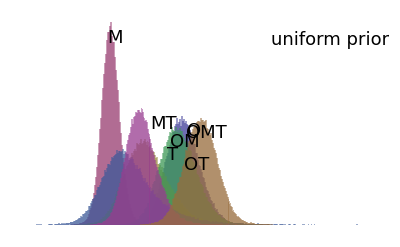

```mathematica
plot=Histogram[T[combodata[[;;,-7-7;;-1-7]]],"FreedmanDiaconis","PDF",ChartLabels->Evaluate[Style[#,18]&/@{"O","M","T","OM","OT","MT","OMT"}],
FrameLabel->{"difference in 3rd moment from no-insomnia distribution","density"},ImageSize->a4longside,PlotRange->All,Epilog->Text[Style["uniform prior",18],Scaled[{0.9,0.9}]]]
```

```mathematica
Export["3rddistances_symptomcombos_unif.pdf",plot,Magnification->1,ImageResolution->400]
```

3rddistances_symptomcombos_unif.pdf

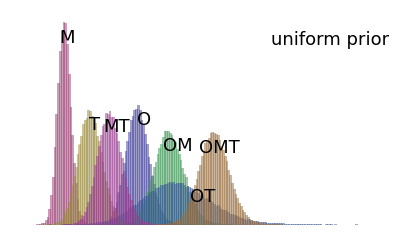

```mathematica
plot=Histogram[T[combodata[[;;,-7-7-7-7;;-1-7-7-7]]],"FreedmanDiaconis","PDF",ChartLabels->Evaluate[Style[#,18]&/@{"O","M","T","OM","OT","MT","OMT"}],
FrameLabel->{"difference in mean from no-insomnia distribution","density"},ImageSize->a4longside,PlotRange->All,Epilog->Text[Style["uniform prior",18],Scaled[{0.9,0.9}]]]
```

```mathematica
Export["meandistances_symptomcombos_unif.pdf",plot,Magnification->1,ImageResolution->400]
```

meandistances_symptomcombos_unif.pdf